### Start choosing the example:

```mathematica
t=22;
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7},Adjacency Matrix→{{0,1,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,1,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,1,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{2,I2}},Exit Vertices and Terminal Costs→{{5,U1},{6,U2},{7,U3}},Switching Costs→{}|>

```mathematica
AdjacencyGraph[Data["Vertices List"],Data["Adjacency Matrix"],VertexLabels->"Name"]
```

-Graphics-

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2,I2->2, U1-> 1,U2->1,U3->0}];//Timing//AbsoluteTiming
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 119.547 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{119.749,{128.976,Null}}

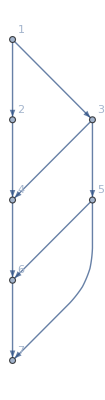
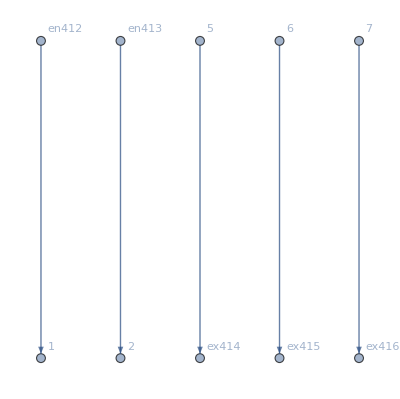
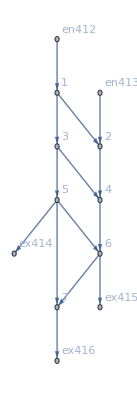
<|BG→-Graphics-,EntranceVertices→{1,2},InwardVertices→<|1→en412,2→en413|>,InEdges→{en412->1,en413->2},ExitVertices→{5,6,7},OutwardVertices→<|5→ex414,6→ex415,7→ex416|>,OutEdges→{5->ex414,6->ex415,7->ex416},AuxiliaryGraph→-Graphics-,FG→-Graphics-,VL→{1,2,3,4,5,6,7},EL→{1->2,1->3,2->4,3->4,3->5,4->6,5->6,5->7,5->ex414,6->7,6->ex415,7->ex416,en412->1,en413->2},BEL→{1->2,1->3,2->4,3->4,3->5,4->6,5->6,5->7,6->7},FVL→{1,2,3,4,5,6,7,en412,en413,ex414,ex415,ex416},AllTransitions→{{1,1->2,1->3},{1,1->2,en412->1},{1,1->3,1->2},{1,1->3,en412->1},{1,en412->1,1->2},{1,en412->1,1->3},{2,1->2,2->4},{2,1->2,en413->2},{2,2->4,1->2},{2,2->4,en413->2},{2,en413->2,1->2},{2,en413->2,2->4},{3,1->3,3->4},{3,1->3,3->5},{3,3->4,1->3},{3,3->4,3->5},{3,3->5,1->3},{3,3->5,3->4},{4,2->4,3->4},{4,2->4,4->6},{4,3->4,2->4},{4,3->4,4->6},{4,4->6,2->4},{4,4->6,3->4},{5,3->5,5->6},{5,3->5,5->7},{5,3->5,5->ex414},{5,5->6,3->5},{5,5->6,5->7},{5,5->6,5->ex414},{5,5->7,3->5},{5,5->7,5->6},{5,5->7,5->ex414},{5,5->ex414,3->5},{5,5->ex414,5->6},{5,5->ex414,5->7},{6,4->6,5->6},{6,4->6,6->7},{6,4->6,6->ex415},{6,5->6,4->6},{6,5->6,6->7},{6,5->6,6->ex415},{6,6->7,4->6},{6,6->7,5->6},{6,6->7,6->ex415},{6,6->ex415,4->6},{6,6->ex415,5->6},{6,6->ex415,6->7},{7,5->7,6->7},{7,5->7,7->ex416},{7,6->7,5->7},{7,6->7,7->ex416},{7,7->ex416,5->7},{7,7->ex416,6->7}},NoDeadEnds→{{1,1->2},{1,1->3},{1,en412->1},{2,1->2},{2,2->4},{2,en413->2},{3,1->3},{3,3->4},{3,3->5},{4,2->4},{4,3->4},{4,4->6},{5,3->5},{5,5->6},{5,5->7},{5,5->ex414},{6,4->6},{6,5->6},{6,6->7},{6,6->ex415},{7,5->7},{7,6->7},{7,7->ex416}},NoDeadStarts→{{2,1->2},{3,1->3},{en412,en412->1},{1,1->2},{4,2->4},{en413,en413->2},{1,1->3},{4,3->4},{5,3->5},{2,2->4},{3,3->4},{6,4->6},{3,3->5},{6,5->6},{7,5->7},{ex414,5->ex414},{4,4->6},{5,5->6},{7,6->7},{ex415,6->ex415},{5,5->7},{6,6->7},{ex416,7->ex416}},jargs→{{2,1->2},{3,1->3},{4,2->4},{4,3->4},{5,3->5},{6,4->6},{6,5->6},{7,5->7},{ex414,5->ex414},{7,6->7},{ex415,6->ex415},{ex416,7->ex416},{1,en412->1},{2,en413->2},{1,1->2},{1,1->3},{2,2->4},{3,3->4},{3,3->5},{4,4->6},{5,5->6},{5,5->7},{5,5->ex414},{6,6->7},{6,6->ex415},{7,7->ex416},{en412,en412->1},{en413,en413->2}},js→{j417,j418,j419,j420,j421,j422,j423,j424,j425,j426,j427,j428,j429,j430,j431,j432,j433,j434,j435,j436,j437,j438,j439,j440,j441,j442,j443,j444},jvars→<|{2,1->2}→j417,{3,1->3}→j418,{4,2->4}→j419,{4,3->4}→j420,{5,3->5}→j421,{6,4->6}→j422,{6,5->6}→j423,{7,5->7}→j424,{ex414,5->ex414}→j425,{7,6->7}→j426,{ex415,6->ex415}→j427,{ex416,7->ex416}→j428,{1,en412->1}→j429,{2,en413->2}→j430,{1,1->2}→j431,{1,1->3}→j432,{2,2->4}→j433,{3,3->4}→j434,{3,3->5}→j435,{4,4->6}→j436,{5,5->6}→j437,{5,5->7}→j438,{5,5->ex414}→j439,{6,6->7}→j440,{6,6->ex415}→j441,{7,7->ex416}→j442,{en412,en412->1}→j443,{en413,en413->2}→j444|>,jts→{jt445,jt446,jt447,jt448,jt449,jt450,jt451,jt452,jt453,jt454,jt455,jt456,jt457,jt458,jt459,jt460,jt461,jt462,jt463,jt464,jt465,jt466,jt467,jt468,jt469,jt470,jt471,jt472,jt473,jt474,jt475,jt476,jt477,jt478,jt479,jt480,jt481,jt482,jt483,jt484,jt485,jt486,jt487,jt488,jt489,jt490,jt491,jt492,jt493,jt494,jt495,jt496,jt497,jt498},jtvars→<|{1,1->2,1->3}→jt445,{1,1->2,en412->1}→jt446,{1,1->3,1->2}→jt447,{1,1->3,en412->1}→jt448,{1,en412->1,1->2}→jt449,{1,en412->1,1->3}→jt450,{2,1->2,2->4}→jt451,{2,1->2,en413->2}→jt452,{2,2->4,1->2}→jt453,{2,2->4,en413->2}→jt454,{2,en413->2,1->2}→jt455,{2,en413->2,2->4}→jt456,{3,1->3,3->4}→jt457,{3,1->3,3->5}→jt458,{3,3->4,1->3}→jt459,{3,3->4,3->5}→jt460,{3,3->5,1->3}→jt461,{3,3->5,3->4}→jt462,{4,2->4,3->4}→jt463,{4,2->4,4->6}→jt464,{4,3->4,2->4}→jt465,{4,3->4,4->6}→jt466,{4,4->6,2->4}→jt467,{4,4->6,3->4}→jt468,{5,3->5,5->6}→jt469,{5,3->5,5->7}→jt470,{5,3->5,5->ex414}→jt471,{5,5->6,3->5}→jt472,{5,5->6,5->7}→jt473,{5,5->6,5->ex414}→jt474,{5,5->7,3->5}→jt475,{5,5->7,5->6}→jt476,{5,5->7,5->ex414}→jt477,{5,5->ex414,3->5}→jt478,{5,5->ex414,5->6}→jt479,{5,5->ex414,5->7}→jt480,{6,4->6,5->6}→jt481,{6,4->6,6->7}→jt482,{6,4->6,6->ex415}→jt483,{6,5->6,4->6}→jt484,{6,5->6,6->7}→jt485,{6,5->6,6->ex415}→jt486,{6,6->7,4->6}→jt487,{6,6->7,5->6}→jt488,{6,6->7,6->ex415}→jt489,{6,6->ex415,4->6}→jt490,{6,6->ex415,5->6}→jt491,{6,6->ex415,6->7}→jt492,{7,5->7,6->7}→jt493,{7,5->7,7->ex416}→jt494,{7,6->7,5->7}→jt495,{7,6->7,7->ex416}→jt496,{7,7->ex416,5->7}→jt497,{7,7->ex416,6->7}→jt498|>,uargs→{{1,1->2},{1,1->3},{2,2->4},{3,3->4},{3,3->5},{4,4->6},{5,5->6},{5,5->7},{5,5->ex414},{6,6->7},{6,6->ex415},{7,7->ex416},{en412,en412->1},{en413,en413->2},{2,1->2},{3,1->3},{4,2->4},{4,3->4},{5,3->5},{6,4->6},{6,5->6},{7,5->7},{ex414,5->ex414},{7,6->7},{ex415,6->ex415},{ex416,7->ex416},{1,en412->1},{2,en413->2}},us→{u499,u500,u501,u502,u503,u504,u505,u506,u507,u508,u509,u510,u511,u512,u513,u514,u515,u516,u517,u518,u519,u520,u521,u522,u523,u524,u525,u526},uvars→<|{1,1->2}→u499,{1,1->3}→u500,{2,2->4}→u501,{3,3->4}→u502,{3,3->5}→u503,{4,4->6}→u504,{5,5->6}→u505,{5,5->7}→u506,{5,5->ex414}→u507,{6,6->7}→u508,{6,6->ex415}→u509,{7,7->ex416}→u510,{en412,en412->1}→u511,{en413,en413->2}→u512,{2,1->2}→u513,{3,1->3}→u514,{4,2->4}→u515,{4,3->4}→u516,{5,3->5}→u517,{6,4->6}→u518,{6,5->6}→u519,{7,5->7}→u520,{ex414,5->ex414}→u521,{7,6->7}→u522,{ex415,6->ex415}→u523,{ex416,7->ex416}→u524,{1,en412->1}→u525,{2,en413->2}→u526|>,SwitchingCosts→<|{1,1->2,1->3}→0,{1,1->2,en412->1}→∞,{1,1->3,1->2}→0,{1,1->3,en412->1}→∞,{1,en412->1,1->2}→0,{1,en412->1,1->3}→0,{2,1->2,2->4}→0,{2,1->2,en413->2}→∞,{2,2->4,1->2}→0,{2,2->4,en413->2}→∞,{2,en413->2,1->2}→0,{2,en413->2,2->4}→0,{3,1->3,3->4}→0,{3,1->3,3->5}→0,{3,3->4,1->3}→0,{3,3->4,3->5}→0,{3,3->5,1->3}→0,{3,3->5,3->4}→0,{4,2->4,3->4}→0,{4,2->4,4->6}→0,{4,3->4,2->4}→0,{4,3->4,4->6}→0,{4,4->6,2->4}→0,{4,4->6,3->4}→0,{5,3->5,5->6}→0,{5,3->5,5->7}→0,{5,3->5,5->ex414}→0,{5,5->6,3->5}→0,{5,5->6,5->7}→0,{5,5->6,5->ex414}→0,{5,5->7,3->5}→0,{5,5->7,5->6}→0,{5,5->7,5->ex414}→0,{5,5->ex414,3->5}→∞,{5,5->ex414,5->6}→∞,{5,5->ex414,5->7}→∞,{6,4->6,5->6}→0,{6,4->6,6->7}→0,{6,4->6,6->ex415}→0,{6,5->6,4->6}→0,{6,5->6,6->7}→0,{6,5->6,6->ex415}→0,{6,6->7,4->6}→0,{6,6->7,5->6}→0,{6,6->7,6->ex415}→0,{6,6->ex415,4->6}→∞,{6,6->ex415,5->6}→∞,{6,6->ex415,6->7}→∞,{7,5->7,6->7}→0,{7,5->7,7->ex416}→0,{7,6->7,5->7}→0,{7,6->7,7->ex416}→0,{7,7->ex416,5->7}→∞,{7,7->ex416,6->7}→∞,{5,5->ex414,1->2}→∞,{5,5->ex414,1->3}→∞,{5,5->ex414,2->4}→∞,{5,5->ex414,3->4}→∞,{5,5->ex414,4->6}→∞,{5,5->ex414,5->ex414}→∞,{5,5->ex414,6->7}→∞,{5,5->ex414,6->ex415}→∞,{5,5->ex414,7->ex416}→∞,{5,5->ex414,en412->1}→∞,{5,5->ex414,en413->2}→∞,{6,6->ex415,1->2}→∞,{6,6->ex415,1->3}→∞,{6,6->ex415,2->4}→∞,{6,6->ex415,3->4}→∞,{6,6->ex415,3->5}→∞,{6,6->ex415,5->7}→∞,{6,6->ex415,5->ex414}→∞,{6,6->ex415,6->ex415}→∞,{6,6->ex415,7->ex416}→∞,{6,6->ex415,en412->1}→∞,{6,6->ex415,en413->2}→∞,{7,7->ex416,1->2}→∞,{7,7->ex416,1->3}→∞,{7,7->ex416,2->4}→∞,{7,7->ex416,3->4}→∞,{7,7->ex416,3->5}→∞,{7,7->ex416,4->6}→∞,{7,7->ex416,5->6}→∞,{7,7->ex416,5->ex414}→∞,{7,7->ex416,6->ex415}→∞,{7,7->ex416,7->ex416}→∞,{7,7->ex416,en412->1}→∞,{7,7->ex416,en413->2}→∞,{2,1->3,en413->2}→∞,{1,en412->1,en412->1}→∞,{2,en412->1,en413->2}→∞,{1,2->4,en412->1}→∞,{1,en413->2,en412->1}→∞,{2,en413->2,en413->2}→∞|>,OutRules→{{5,5->ex414,1->2}→∞,{5,5->ex414,1->3}→∞,{5,5->ex414,2->4}→∞,{5,5->ex414,3->4}→∞,{5,5->ex414,3->5}→∞,{5,5->ex414,4->6}→∞,{5,5->ex414,5->6}→∞,{5,5->ex414,5->7}→∞,{5,5->ex414,5->ex414}→∞,{5,5->ex414,6->7}→∞,{5,5->ex414,6->ex415}→∞,{5,5->ex414,7->ex416}→∞,{5,5->ex414,en412->1}→∞,{5,5->ex414,en413->2}→∞,{6,6->ex415,1->2}→∞,{6,6->ex415,1->3}→∞,{6,6->ex415,2->4}→∞,{6,6->ex415,3->4}→∞,{6,6->ex415,3->5}→∞,{6,6->ex415,4->6}→∞,{6,6->ex415,5->6}→∞,{6,6->ex415,5->7}→∞,{6,6->ex415,5->ex414}→∞,{6,6->ex415,6->7}→∞,{6,6->ex415,6->ex415}→∞,{6,6->ex415,7->ex416}→∞,{6,6->ex415,en412->1}→∞,{6,6->ex415,en413->2}→∞,{7,7->ex416,1->2}→∞,{7,7->ex416,1->3}→∞,{7,7->ex416,2->4}→∞,{7,7->ex416,3->4}→∞,{7,7->ex416,3->5}→∞,{7,7->ex416,4->6}→∞,{7,7->ex416,5->6}→∞,{7,7->ex416,5->7}→∞,{7,7->ex416,5->ex414}→∞,{7,7->ex416,6->7}→∞,{7,7->ex416,6->ex415}→∞,{7,7->ex416,7->ex416}→∞,{7,7->ex416,en412->1}→∞,{7,7->ex416,en413->2}→∞},InRules→{{1,1->2,en412->1}→∞,{2,1->2,en413->2}→∞,{1,1->3,en412->1}→∞,{2,1->3,en413->2}→∞,{1,en412->1,en412->1}→∞,{2,en412->1,en413->2}→∞,{1,1->2,en412->1}→∞,{2,1->2,en413->2}→∞,{1,2->4,en412->1}→∞,{2,2->4,en413->2}→∞,{1,en413->2,en412->1}→∞,{2,en413->2,en413->2}→∞},EntryArgs→{{1,en412->1},{2,en413->2}},EntryDataAssociation→<|{1,en412->1}→2,{2,en413->2}→2|>,jays→<|1->2→j417-j431,1->3→j418-j432,2->4→j419-j433,3->4→j420-j434,3->5→j421-j435,4->6→j422-j436,5->6→j423-j437,5->7→j424-j438,6->7→j426-j440|>,NonZeroEntryCurrents→True,ExitCosts→<|ex414→1,ex415→1,ex416→0|>,EqCurrentCompCon→(j431==0||j417==0)&&(j432==0||j418==0)&&(j433==0||j419==0)&&(j434==0||j420==0)&&(j435==0||j421==0)&&(j436==0||j422==0)&&(j437==0||j423==0)&&(j438==0||j424==0)&&(j439==0||j425==0)&&(j440==0||j426==0)&&(j441==0||j427==0)&&(j442==0||j428==0)&&(j443==0||j429==0)&&(j444==0||j430==0),EqTransitionCompCon→(jt445==0||jt447==0)&&(jt446==0||jt449==0)&&(jt448==0||jt450==0)&&(jt451==0||jt453==0)&&(jt452==0||jt455==0)&&(jt454==0||jt456==0)&&(jt457==0||jt459==0)&&(jt458==0||jt461==0)&&(jt460==0||jt462==0)&&(jt463==0||jt465==0)&&(jt464==0||jt467==0)&&(jt466==0||jt468==0)&&(jt469==0||jt472==0)&&(jt470==0||jt475==0)&&(jt471==0||jt478==0)&&(jt473==0||jt476==0)&&(jt474==0||jt479==0)&&(jt477==0||jt480==0)&&(jt481==0||jt484==0)&&(jt482==0||jt487==0)&&(jt483==0||jt490==0)&&(jt485==0||jt488==0)&&(jt486==0||jt491==0)&&(jt489==0||jt492==0)&&(jt493==0||jt495==0)&&(jt494==0||jt497==0)&&(jt496==0||jt498==0),EqCompCon→(jt445==0||-u499+u500==0)&&jt446==0&&(jt447==0||u499-u500==0)&&jt448==0&&(jt449==0||u499-u525==0)&&(jt450==0||u500-u525==0)&&(jt451==0||u501-u513==0)&&jt452==0&&(jt453==0||-u501+u513==0)&&jt454==0&&(jt455==0||u513-u526==0)&&(jt456==0||u501-u526==0)&&(jt457==0||u502-u514==0)&&(jt458==0||u503-u514==0)&&(jt459==0||-u502+u514==0)&&(jt460==0||-u502+u503==0)&&(jt461==0||-u503+u514==0)&&(jt462==0||u502-u503==0)&&(jt463==0||-u515+u516==0)&&(jt464==0||u504-u515==0)&&(jt465==0||u515-u516==0)&&(jt466==0||u504-u516==0)&&(jt467==0||-u504+u515==0)&&(jt468==0||-u504+u516==0)&&(jt469==0||u505-u517==0)&&(jt470==0||u506-u517==0)&&(jt471==0||u507-u517==0)&&(jt472==0||-u505+u517==0)&&(jt473==0||-u505+u506==0)&&(jt474==0||-u505+u507==0)&&(jt475==0||-u506+u517==0)&&(jt476==0||u505-u506==0)&&(jt477==0||-u506+u507==0)&&jt478==0&&jt479==0&&jt480==0&&(jt481==0||-u518+u519==0)&&(jt482==0||u508-u518==0)&&(jt483==0||u509-u518==0)&&(jt484==0||u518-u519==0)&&(jt485==0||u508-u519==0)&&(jt486==0||u509-u519==0)&&(jt487==0||-u508+u518==0)&&(jt488==0||-u508+u519==0)&&(jt489==0||-u508+u509==0)&&jt490==0&&jt491==0&&jt492==0&&(jt493==0||-u520+u522==0)&&(jt494==0||u510-u520==0)&&(jt495==0||u520-u522==0)&&(jt496==0||u510-u522==0)&&jt497==0&&jt498==0,EqAllComp→(j431==0||j417==0)&&(j432==0||j418==0)&&(j433==0||j419==0)&&(j434==0||j420==0)&&(j435==0||j421==0)&&(j436==0||j422==0)&&(j437==0||j423==0)&&(j438==0||j424==0)&&(j439==0||j425==0)&&(j440==0||j426==0)&&(j441==0||j427==0)&&(j442==0||j428==0)&&(j443==0||j429==0)&&(j444==0||j430==0)&&(jt445==0||jt447==0)&&(jt446==0||jt449==0)&&(jt448==0||jt450==0)&&(jt451==0||jt453==0)&&(jt452==0||jt455==0)&&(jt454==0||jt456==0)&&(jt457==0||jt459==0)&&(jt458==0||jt461==0)&&(jt460==0||jt462==0)&&(jt463==0||jt465==0)&&(jt464==0||jt467==0)&&(jt466==0||jt468==0)&&(jt469==0||jt472==0)&&(jt470==0||jt475==0)&&(jt471==0||jt478==0)&&(jt473==0||jt476==0)&&(jt474==0||jt479==0)&&(jt477==0||jt480==0)&&(jt481==0||jt484==0)&&(jt482==0||jt487==0)&&(jt483==0||jt490==0)&&(jt485==0||jt488==0)&&(jt486==0||jt491==0)&&(jt489==0||jt492==0)&&(jt493==0||jt495==0)&&(jt494==0||jt497==0)&&(jt496==0||jt498==0)&&(jt445==0||-u499+u500==0)&&jt446==0&&(jt447==0||u499-u500==0)&&jt448==0&&(jt449==0||u499-u525==0)&&(jt450==0||u500-u525==0)&&(jt451==0||u501-u513==0)&&jt452==0&&(jt453==0||-u501+u513==0)&&jt454==0&&(jt455==0||u513-u526==0)&&(jt456==0||u501-u526==0)&&(jt457==0||u502-u514==0)&&(jt458==0||u503-u514==0)&&(jt459==0||-u502+u514==0)&&(jt460==0||-u502+u503==0)&&(jt461==0||-u503+u514==0)&&(jt462==0||u502-u503==0)&&(jt463==0||-u515+u516==0)&&(jt464==0||u504-u515==0)&&(jt465==0||u515-u516==0)&&(jt466==0||u504-u516==0)&&(jt467==0||-u504+u515==0)&&(jt468==0||-u504+u516==0)&&(jt469==0||u505-u517==0)&&(jt470==0||u506-u517==0)&&(jt471==0||u507-u517==0)&&(jt472==0||-u505+u517==0)&&(jt473==0||-u505+u506==0)&&(jt474==0||-u505+u507==0)&&(jt475==0||-u506+u517==0)&&(jt476==0||u505-u506==0)&&(jt477==0||-u506+u507==0)&&jt478==0&&jt479==0&&jt480==0&&(jt481==0||-u518+u519==0)&&(jt482==0||u508-u518==0)&&(jt483==0||u509-u518==0)&&(jt484==0||u518-u519==0)&&(jt485==0||u508-u519==0)&&(jt486==0||u509-u519==0)&&(jt487==0||-u508+u518==0)&&(jt488==0||-u508+u519==0)&&(jt489==0||-u508+u509==0)&&jt490==0&&jt491==0&&jt492==0&&(jt493==0||-u520+u522==0)&&(jt494==0||u510-u520==0)&&(jt495==0||u520-u522==0)&&(jt496==0||u510-u522==0)&&jt497==0&&jt498==0,EqPosCon→NonNegative[j417]&&NonNegative[j418]&&NonNegative[j419]&&NonNegative[j420]&&NonNegative[j421]&&NonNegative[j422]&&NonNegative[j423]&&NonNegative[j424]&&NonNegative[j425]&&NonNegative[j426]&&NonNegative[j427]&&NonNegative[j428]&&NonNegative[j429]&&NonNegative[j430]&&NonNegative[j431]&&NonNegative[j432]&&NonNegative[j433]&&NonNegative[j434]&&NonNegative[j435]&&NonNegative[j436]&&NonNegative[j437]&&NonNegative[j438]&&NonNegative[j439]&&NonNegative[j440]&&NonNegative[j441]&&NonNegative[j442]&&NonNegative[j443]&&NonNegative[j444]&&NonNegative[jt445]&&NonNegative[jt446]&&NonNegative[jt447]&&NonNegative[jt448]&&NonNegative[jt449]&&NonNegative[jt450]&&NonNegative[jt451]&&NonNegative[jt452]&&NonNegative[jt453]&&NonNegative[jt454]&&NonNegative[jt455]&&NonNegative[jt456]&&NonNegative[jt457]&&NonNegative[jt458]&&NonNegative[jt459]&&NonNegative[jt460]&&NonNegative[jt461]&&NonNegative[jt462]&&NonNegative[jt463]&&NonNegative[jt464]&&NonNegative[jt465]&&NonNegative[jt466]&&NonNegative[jt467]&&NonNegative[jt468]&&NonNegative[jt469]&&NonNegative[jt470]&&NonNegative[jt471]&&NonNegative[jt472]&&NonNegative[jt473]&&NonNegative[jt474]&&NonNegative[jt475]&&NonNegative[jt476]&&NonNegative[jt477]&&NonNegative[jt478]&&NonNegative[jt479]&&NonNegative[jt480]&&NonNegative[jt481]&&NonNegative[jt482]&&NonNegative[jt483]&&NonNegative[jt484]&&NonNegative[jt485]&&NonNegative[jt486]&&NonNegative[jt487]&&NonNegative[jt488]&&NonNegative[jt489]&&NonNegative[jt490]&&NonNegative[jt491]&&NonNegative[jt492]&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&NonNegative[jt496]&&NonNegative[jt497]&&NonNegative[jt498],EqBalanceSplittingCurrents→j431==jt445+jt446&&j432==jt447+jt448&&j429==jt449+jt450&&j417==jt451+jt452&&j433==jt453+jt454&&j430==jt455+jt456&&j418==jt457+jt458&&j434==jt459+jt460&&j435==jt461+jt462&&j419==jt463+jt464&&j420==jt465+jt466&&j436==jt467+jt468&&j421==jt469+jt470+jt471&&j437==jt472+jt473+jt474&&j438==jt475+jt476+jt477&&j439==jt478+jt479+jt480&&j422==jt481+jt482+jt483&&j423==jt484+jt485+jt486&&j440==jt487+jt488+jt489&&j441==jt490+jt491+jt492&&j424==jt493+jt494&&j426==jt495+jt496&&j442==jt497+jt498,EqBalanceGatheringCurrents→j417==jt447+jt449&&j418==jt445+jt450&&j443==jt446+jt448&&j431==jt453+jt455&&j419==jt451+jt456&&j444==jt452+jt454&&j432==jt459+jt461&&j420==jt457+jt462&&j421==jt458+jt460&&j433==jt465+jt467&&j434==jt463+jt468&&j422==jt464+jt466&&j435==jt472+jt475+jt478&&j423==jt469+jt476+jt479&&j424==jt470+jt473+jt480&&j425==jt471+jt474+jt477&&j436==jt484+jt487+jt490&&j437==jt481+jt488+jt491&&j426==jt482+jt485+jt492&&j427==jt483+jt486+jt489&&j438==jt495+jt497&&j440==jt493+jt498&&j428==jt494+jt496,EqEntryIn→j429==2&&j430==2,EqExitValues→u521==1&&u523==1&&u524==0,EqSwitchingConditions→u500≥u525&&u499==u500&&u513≥u526&&u501==u513&&u503==u514&&u502==u514&&u515==u516&&u504==u515&&u507≥u517&&u506==u517&&u505==u517&&u509≥u519&&u518==u519&&u508==u519&&u510≥u522&&u520==u522,EqValueAuxiliaryEdges→-u511+u525==0&&-u512+u526==0&&-u507+u521==0&&-u509+u523==0&&-u510+u524==0,EqAll→NonNegative[j417]&&NonNegative[j418]&&NonNegative[j419]&&NonNegative[j420]&&NonNegative[j421]&&NonNegative[j422]&&NonNegative[j423]&&NonNegative[j424]&&NonNegative[j425]&&NonNegative[j426]&&NonNegative[j427]&&NonNegative[j428]&&NonNegative[j429]&&NonNegative[j430]&&NonNegative[j431]&&NonNegative[j432]&&NonNegative[j433]&&NonNegative[j434]&&NonNegative[j435]&&NonNegative[j436]&&NonNegative[j437]&&NonNegative[j438]&&NonNegative[j439]&&NonNegative[j440]&&NonNegative[j441]&&NonNegative[j442]&&NonNegative[j443]&&NonNegative[j444]&&NonNegative[jt445]&&NonNegative[jt446]&&NonNegative[jt447]&&NonNegative[jt448]&&NonNegative[jt449]&&NonNegative[jt450]&&NonNegative[jt451]&&NonNegative[jt452]&&NonNegative[jt453]&&NonNegative[jt454]&&NonNegative[jt455]&&NonNegative[jt456]&&NonNegative[jt457]&&NonNegative[jt458]&&NonNegative[jt459]&&NonNegative[jt460]&&NonNegative[jt461]&&NonNegative[jt462]&&NonNegative[jt463]&&NonNegative[jt464]&&NonNegative[jt465]&&NonNegative[jt466]&&NonNegative[jt467]&&NonNegative[jt468]&&NonNegative[jt469]&&NonNegative[jt470]&&NonNegative[jt471]&&NonNegative[jt472]&&NonNegative[jt473]&&NonNegative[jt474]&&NonNegative[jt475]&&NonNegative[jt476]&&NonNegative[jt477]&&NonNegative[jt478]&&NonNegative[jt479]&&NonNegative[jt480]&&NonNegative[jt481]&&NonNegative[jt482]&&NonNegative[jt483]&&NonNegative[jt484]&&NonNegative[jt485]&&NonNegative[jt486]&&NonNegative[jt487]&&NonNegative[jt488]&&NonNegative[jt489]&&NonNegative[jt490]&&NonNegative[jt491]&&NonNegative[jt492]&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&NonNegative[jt496]&&NonNegative[jt497]&&NonNegative[jt498]&&j431==jt445+jt446&&j432==jt447+jt448&&j429==jt449+jt450&&j417==jt451+jt452&&j433==jt453+jt454&&j430==jt455+jt456&&j418==jt457+jt458&&j434==jt459+jt460&&j435==jt461+jt462&&j419==jt463+jt464&&j420==jt465+jt466&&j436==jt467+jt468&&j421==jt469+jt470+jt471&&j437==jt472+jt473+jt474&&j438==jt475+jt476+jt477&&j439==jt478+jt479+jt480&&j422==jt481+jt482+jt483&&j423==jt484+jt485+jt486&&j440==jt487+jt488+jt489&&j441==jt490+jt491+jt492&&j424==jt493+jt494&&j426==jt495+jt496&&j442==jt497+jt498&&j417==jt447+jt449&&j418==jt445+jt450&&j443==jt446+jt448&&j431==jt453+jt455&&j419==jt451+jt456&&j444==jt452+jt454&&j432==jt459+jt461&&j420==jt457+jt462&&j421==jt458+jt460&&j433==jt465+jt467&&j434==jt463+jt468&&j422==jt464+jt466&&j435==jt472+jt475+jt478&&j423==jt469+jt476+jt479&&j424==jt470+jt473+jt480&&j425==jt471+jt474+jt477&&j436==jt484+jt487+jt490&&j437==jt481+jt488+jt491&&j426==jt482+jt485+jt492&&j427==jt483+jt486+jt489&&j438==jt495+jt497&&j440==jt493+jt498&&j428==jt494+jt496&&j429==2&&j430==2&&u521==1&&u523==1&&u524==0&&u500≥u525&&u499==u500&&u513≥u526&&u501==u513&&u503==u514&&u502==u514&&u515==u516&&u504==u515&&u507≥u517&&u506==u517&&u505==u517&&u509≥u519&&u518==u519&&u508==u519&&u510≥u522&&u520==u522&&-u511+u525==0&&-u512+u526==0&&-u507+u521==0&&-u509+u523==0&&-u510+u524==0,EqAllAll→NonNegative[j417]&&NonNegative[j418]&&NonNegative[j419]&&NonNegative[j420]&&NonNegative[j421]&&NonNegative[j422]&&NonNegative[j423]&&NonNegative[j424]&&NonNegative[j425]&&NonNegative[j426]&&NonNegative[j427]&&NonNegative[j428]&&NonNegative[j429]&&NonNegative[j430]&&NonNegative[j431]&&NonNegative[j432]&&NonNegative[j433]&&NonNegative[j434]&&NonNegative[j435]&&NonNegative[j436]&&NonNegative[j437]&&NonNegative[j438]&&NonNegative[j439]&&NonNegative[j440]&&NonNegative[j441]&&NonNegative[j442]&&NonNegative[j443]&&NonNegative[j444]&&NonNegative[jt445]&&NonNegative[jt446]&&NonNegative[jt447]&&NonNegative[jt448]&&NonNegative[jt449]&&NonNegative[jt450]&&NonNegative[jt451]&&NonNegative[jt452]&&NonNegative[jt453]&&NonNegative[jt454]&&NonNegative[jt455]&&NonNegative[jt456]&&NonNegative[jt457]&&NonNegative[jt458]&&NonNegative[jt459]&&NonNegative[jt460]&&NonNegative[jt461]&&NonNegative[jt462]&&NonNegative[jt463]&&NonNegative[jt464]&&NonNegative[jt465]&&NonNegative[jt466]&&NonNegative[jt467]&&NonNegative[jt468]&&NonNegative[jt469]&&NonNegative[jt470]&&NonNegative[jt471]&&NonNegative[jt472]&&NonNegative[jt473]&&NonNegative[jt474]&&NonNegative[jt475]&&NonNegative[jt476]&&NonNegative[jt477]&&NonNegative[jt478]&&NonNegative[jt479]&&NonNegative[jt480]&&NonNegative[jt481]&&NonNegative[jt482]&&NonNegative[jt483]&&NonNegative[jt484]&&NonNegative[jt485]&&NonNegative[jt486]&&NonNegative[jt487]&&NonNegative[jt488]&&NonNegative[jt489]&&NonNegative[jt490]&&NonNegative[jt491]&&NonNegative[jt492]&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&NonNegative[jt496]&&NonNegative[jt497]&&NonNegative[jt498]&&j431==jt445+jt446&&j432==jt447+jt448&&j429==jt449+jt450&&j417==jt451+jt452&&j433==jt453+jt454&&j430==jt455+jt456&&j418==jt457+jt458&&j434==jt459+jt460&&j435==jt461+jt462&&j419==jt463+jt464&&j420==jt465+jt466&&j436==jt467+jt468&&j421==jt469+jt470+jt471&&j437==jt472+jt473+jt474&&j438==jt475+jt476+jt477&&j439==jt478+jt479+jt480&&j422==jt481+jt482+jt483&&j423==jt484+jt485+jt486&&j440==jt487+jt488+jt489&&j441==jt490+jt491+jt492&&j424==jt493+jt494&&j426==jt495+jt496&&j442==jt497+jt498&&j417==jt447+jt449&&j418==jt445+jt450&&j443==jt446+jt448&&j431==jt453+jt455&&j419==jt451+jt456&&j444==jt452+jt454&&j432==jt459+jt461&&j420==jt457+jt462&&j421==jt458+jt460&&j433==jt465+jt467&&j434==jt463+jt468&&j422==jt464+jt466&&j435==jt472+jt475+jt478&&j423==jt469+jt476+jt479&&j424==jt470+jt473+jt480&&j425==jt471+jt474+jt477&&j436==jt484+jt487+jt490&&j437==jt481+jt488+jt491&&j426==jt482+jt485+jt492&&j427==jt483+jt486+jt489&&j438==jt495+jt497&&j440==jt493+jt498&&j428==jt494+jt496&&j429==2&&j430==2&&u521==1&&u523==1&&u524==0&&u500≥u525&&u499==u500&&u513≥u526&&u501==u513&&u503==u514&&u502==u514&&u515==u516&&u504==u515&&u507≥u517&&u506==u517&&u505==u517&&u509≥u519&&u518==u519&&u508==u519&&u510≥u522&&u520==u522&&-u511+u525==0&&-u512+u526==0&&-u507+u521==0&&-u509+u523==0&&-u510+u524==0&&(j431==0||j417==0)&&(j432==0||j418==0)&&(j433==0||j419==0)&&(j434==0||j420==0)&&(j435==0||j421==0)&&(j436==0||j422==0)&&(j437==0||j423==0)&&(j438==0||j424==0)&&(j439==0||j425==0)&&(j440==0||j426==0)&&(j441==0||j427==0)&&(j442==0||j428==0)&&(j443==0||j429==0)&&(j444==0||j430==0)&&(jt445==0||jt447==0)&&(jt446==0||jt449==0)&&(jt448==0||jt450==0)&&(jt451==0||jt453==0)&&(jt452==0||jt455==0)&&(jt454==0||jt456==0)&&(jt457==0||jt459==0)&&(jt458==0||jt461==0)&&(jt460==0||jt462==0)&&(jt463==0||jt465==0)&&(jt464==0||jt467==0)&&(jt466==0||jt468==0)&&(jt469==0||jt472==0)&&(jt470==0||jt475==0)&&(jt471==0||jt478==0)&&(jt473==0||jt476==0)&&(jt474==0||jt479==0)&&(jt477==0||jt480==0)&&(jt481==0||jt484==0)&&(jt482==0||jt487==0)&&(jt483==0||jt490==0)&&(jt485==0||jt488==0)&&(jt486==0||jt491==0)&&(jt489==0||jt492==0)&&(jt493==0||jt495==0)&&(jt494==0||jt497==0)&&(jt496==0||jt498==0)&&(jt445==0||-u499+u500==0)&&jt446==0&&(jt447==0||u499-u500==0)&&jt448==0&&(jt449==0||u499-u525==0)&&(jt450==0||u500-u525==0)&&(jt451==0||u501-u513==0)&&jt452==0&&(jt453==0||-u501+u513==0)&&jt454==0&&(jt455==0||u513-u526==0)&&(jt456==0||u501-u526==0)&&(jt457==0||u502-u514==0)&&(jt458==0||u503-u514==0)&&(jt459==0||-u502+u514==0)&&(jt460==0||-u502+u503==0)&&(jt461==0||-u503+u514==0)&&(jt462==0||u502-u503==0)&&(jt463==0||-u515+u516==0)&&(jt464==0||u504-u515==0)&&(jt465==0||u515-u516==0)&&(jt466==0||u504-u516==0)&&(jt467==0||-u504+u515==0)&&(jt468==0||-u504+u516==0)&&(jt469==0||u505-u517==0)&&(jt470==0||u506-u517==0)&&(jt471==0||u507-u517==0)&&(jt472==0||-u505+u517==0)&&(jt473==0||-u505+u506==0)&&(jt474==0||-u505+u507==0)&&(jt475==0||-u506+u517==0)&&(jt476==0||u505-u506==0)&&(jt477==0||-u506+u507==0)&&jt478==0&&jt479==0&&jt480==0&&(jt481==0||-u518+u519==0)&&(jt482==0||u508-u518==0)&&(jt483==0||u509-u518==0)&&(jt484==0||u518-u519==0)&&(jt485==0||u508-u519==0)&&(jt486==0||u509-u519==0)&&(jt487==0||-u508+u518==0)&&(jt488==0||-u508+u519==0)&&(jt489==0||-u508+u509==0)&&jt490==0&&jt491==0&&jt492==0&&(jt493==0||-u520+u522==0)&&(jt494==0||u510-u520==0)&&(jt495==0||u520-u522==0)&&(jt496==0||u510-u522==0)&&jt497==0&&jt498==0,BoundaryRules→{j429→2,j430→2,u521→1,u523→1,u524→0},RulesEntryIn→{j429→2,j430→2},RulesExitValues→{u521→1,u523→1,u524→0},Nlhs→{j417-j431-u499+u513,j418-j432-u500+u514,j419-j433-u501+u515,j420-j434-u502+u516,j421-j435-u503+u517,j422-j436-u504+u518,j423-j437-u505+u519,j424-j438-u506+u520,j426-j440-u508+u522},EqCriticalCase→j417-j431-u499+u513==0&&j418-j432-u500+u514==0&&j419-j433-u501+u515==0&&j420-j434-u502+u516==0&&j421-j435-u503+u517==0&&j422-j436-u504+u518==0&&j423-j437-u505+u519==0&&j424-j438-u506+u520==0&&j426-j440-u508+u522==0,criticalreduced1→{True,<|j417→0,j418→2,j420→0,j421→2,j425→1,j427→1,j428→2,j429→2,j430→2,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j441→0,j442→0,j443→0,j444→0,jt445→0,jt446→0,jt447→0,jt448→0,jt449→0,jt450→2,jt452→0,jt453→0,jt454→0,jt455→0,jt456→2,jt459→0,jt460→0,jt461→0,jt462→0,jt463→0,jt465→0,jt466→0,jt468→0,jt471→1,jt473→0,jt474→0,jt476→0,jt477→0,jt478→0,jt479→0,jt480→0,jt481→0,jt483→1,jt484→0,jt485→0,jt486→0,jt489→0,jt490→0,jt491→0,jt492→0,jt493→0,jt494→1,jt496→1,jt497→0,jt498→0,u499→5,u500→5,u501→5,u502→3,u503→3,u504→3,u505→1,u506→1,u507→1,u509→1,u510→0,u513→5,u514→3,u515→3,u516→3,u517→1,u518→1,u519→1,u520→0,u521→1,u522→0,u523→1,u524→0,u525→5,u526→5,j419→2,j422→2,j423→0,j424→1,j426→1,j440→0,jt451→0,jt457→0,jt458→2,jt464→2,jt467→0,jt469→0,jt470→1,jt472→0,jt475→0,jt482→1,jt487→0,jt488→0,jt495→0,u508→1,u511→5,u512→5|>},Nrhs→{j417-j431+IntM[j417-j431,1->2],j418-j432+IntM[j418-j432,1->3],j419-j433+IntM[j419-j433,2->4],j420-j434+IntM[j420-j434,3->4],j421-j435+IntM[j421-j435,3->5],j422-j436+IntM[j422-j436,4->6],j423-j437+IntM[j423-j437,5->6],j424-j438+IntM[j424-j438,5->7],j426-j440+IntM[j426-j440,6->7]},EqGeneralCase→j417-j431-u499+u513==j417-j431+IntM[j417-j431,1->2]&&j418-j432-u500+u514==j418-j432+IntM[j418-j432,1->3]&&j419-j433-u501+u515==j419-j433+IntM[j419-j433,2->4]&&j420-j434-u502+u516==j420-j434+IntM[j420-j434,3->4]&&j421-j435-u503+u517==j421-j435+IntM[j421-j435,3->5]&&j422-j436-u504+u518==j422-j436+IntM[j422-j436,4->6]&&j423-j437-u505+u519==j423-j437+IntM[j423-j437,5->6]&&j424-j438-u506+u520==j424-j438+IntM[j424-j438,5->7]&&j426-j440-u508+u522==j426-j440+IntM[j426-j440,6->7],TOL→1/1000000|>

```mathematica
MFGEquations
```

```mathematica
MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]
```

<|{2,1->2}→0,{3,1->3}→53/26,{4,2->4}→51/26,{4,3->4}→0,{5,3->5}→28/13,{6,4->6}→24/13,{6,5->6}→0,{7,5->7}→1,{ex239,5->ex239}→41/26,{7,6->7}→37/26,{ex240,6->ex240}→0,{ex241,7->ex241}→63/26,{1,en237->1}→2,{2,en238->2}→2,{1,1->2}→1/26,{1,1->3}→0,{2,2->4}→0,{3,3->4}→3/26,{3,3->5}→0,{4,4->6}→0,{5,5->6}→11/26,{5,5->7}→0,{5,5->ex239}→0,{6,6->7}→0,{6,6->ex240}→0,{7,7->ex241}→0,{en237,en237->1}→0,{en238,en238->2}→0|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}];//Timing//AbsoluteTiming
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 102.257 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{102.402,{111.931,Null}}

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];//Timing//AbsoluteTiming
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 104.37 seconds to reduce with NewReduce!

DataToEquations: Mixed system:

DataToEquations: Possible multiple solutions 
{0≤jt355≤1,<|j302→0,j303→39/11,j305→0,j306→46/11,j310→46/11,j312→9/11,j313→3,j314→2,j315→6,j316→17/11,j317→0,j318→0,j319→7/11,j320→0,j321→0,j322→1,j323→0,j324→0,j326→0,j327→0,j328→0,j329→0,jt330→17/11,jt331→0,jt332→0,jt333→0,jt334→0,jt335→2,jt337→0,jt338→0,jt339→0,jt340→17/11,jt341→49/11,jt344→0,jt345→7/11,jt346→0,jt347→0,jt348→7/11,jt350→0,jt351→0,jt353→0,jt356→46/11-jt355,jt358→1-jt355,jt359→jt355,jt361→0,jt362→0,jt363→0,jt364→0,jt365→0,jt366→1,jt368→9/11,jt369→0,jt370→0,jt371→0,jt374→0,jt375→0,jt376→0,jt377→0,jt378→0,jt379→1,jt381→2,jt382→0,jt383→0,u384→96/11,u385→96/11,u386→113/11,u387→57/11,u388→57/11,u389→64/11,u390→1,u391→1,u392→1,u394→2,u395→0,u398→113/11,u399→57/11,u400→64/11,u401→64/11,u402→1,u403→2,u404→2,u405→0,u406→1,u407→0,u408→2,u409→0,u410→96/11,u411→113/11,j304→49/11,j307→42/11,j308→0,j309→1,j311→2,j325→0,jt336→0,jt342→0,jt343→39/11,jt349→42/11,jt352→0,jt354→0,jt357→0,jt360→0,jt367→2,jt372→0,jt373→0,jt380→0,u393→2,u396→96/11,u397→113/11|>}

DataToEquations: There are multiple solutions for the given data.

DataToEquations: Done.

{104.57,{112.413,Null}}

<|{1,1->2,1->3}→17/11,{1,1->2,en297->1}→0,{1,1->3,1->2}→0,{1,1->3,en297->1}→0,{1,en297->1,1->2}→0,{1,en297->1,1->3}→2,{2,1->2,2->4}→0,{2,1->2,en298->2}→0,{2,2->4,1->2}→0,{2,2->4,en298->2}→0,{2,en298->2,1->2}→17/11,{2,en298->2,2->4}→49/11,{3,1->3,3->4}→0,{3,1->3,3->5}→39/11,{3,3->4,1->3}→0,{3,3->4,3->5}→7/11,{3,3->5,1->3}→0,{3,3->5,3->4}→0,{4,2->4,3->4}→7/11,{4,2->4,4->6}→42/11,{4,3->4,2->4}→0,{4,3->4,4->6}→0,{4,4->6,2->4}→0,{4,4->6,3->4}→0,{5,3->5,5->6}→0,{5,3->5,5->7}→jt355,{5,3->5,5->ex299}→46/11-jt355,{5,5->6,3->5}→0,{5,5->6,5->7}→1-jt355,{5,5->6,5->ex299}→jt355,{5,5->7,3->5}→0,{5,5->7,5->6}→0,{5,5->7,5->ex299}→0,{5,5->ex299,3->5}→0,{5,5->ex299,5->6}→0,{5,5->ex299,5->7}→0,{6,4->6,5->6}→1,{6,4->6,6->7}→2,{6,4->6,6->ex300}→9/11,{6,5->6,4->6}→0,{6,5->6,6->7}→0,{6,5->6,6->ex300}→0,{6,6->7,4->6}→0,{6,6->7,5->6}→0,{6,6->7,6->ex300}→0,{6,6->ex300,4->6}→0,{6,6->ex300,5->6}→0,{6,6->ex300,6->7}→0,{7,5->7,6->7}→0,{7,5->7,7->ex301}→1,{7,6->7,5->7}→0,{7,6->7,7->ex301}→2,{7,7->ex301,5->7}→0,{7,7->ex301,6->7}→0|>

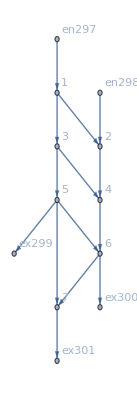

```mathematica
MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]
MFGEquations["FG"]
```

```mathematica
MFGEquations["EqAll"]/.(MFGEquations["criticalreduced1"][[2]])
```

True

```mathematica
MFGEquations["EqAllAll"]
```

NonNegative[j998]&&NonNegative[j999]&&NonNegative[j1000]&&NonNegative[j1001]&&NonNegative[j1002]&&NonNegative[j1003]&&NonNegative[j1004]&&NonNegative[j1005]&&NonNegative[j1006]&&NonNegative[j1007]&&NonNegative[j1008]&&NonNegative[j1009]&&NonNegative[j1010]&&NonNegative[j1011]&&NonNegative[j1012]&&NonNegative[j1013]&&NonNegative[j1014]&&NonNegative[j1015]&&NonNegative[j1016]&&NonNegative[j1017]&&NonNegative[j1018]&&NonNegative[j1019]&&NonNegative[j1020]&&NonNegative[j1021]&&NonNegative[j1022]&&NonNegative[j1023]&&NonNegative[j1024]&&NonNegative[j1025]&&NonNegative[jt1026]&&NonNegative[jt1027]&&NonNegative[jt1028]&&NonNegative[jt1029]&&NonNegative[jt1030]&&NonNegative[jt1031]&&NonNegative[jt1032]&&NonNegative[jt1033]&&NonNegative[jt1034]&&NonNegative[jt1035]&&NonNegative[jt1036]&&NonNegative[jt1037]&&NonNegative[jt1038]&&NonNegative[jt1039]&&NonNegative[jt1040]&&NonNegative[jt1041]&&NonNegative[jt1042]&&NonNegative[jt1043]&&NonNegative[jt1044]&&NonNegative[jt1045]&&NonNegative[jt1046]&&NonNegative[jt1047]&&NonNegative[jt1048]&&NonNegative[jt1049]&&NonNegative[jt1050]&&NonNegative[jt1051]&&NonNegative[jt1052]&&NonNegative[jt1053]&&NonNegative[jt1054]&&NonNegative[jt1055]&&NonNegative[jt1056]&&NonNegative[jt1057]&&NonNegative[jt1058]&&NonNegative[jt1059]&&NonNegative[jt1060]&&NonNegative[jt1061]&&NonNegative[jt1062]&&NonNegative[jt1063]&&NonNegative[jt1064]&&NonNegative[jt1065]&&NonNegative[jt1066]&&NonNegative[jt1067]&&NonNegative[jt1068]&&NonNegative[jt1069]&&NonNegative[jt1070]&&NonNegative[jt1071]&&NonNegative[jt1072]&&NonNegative[jt1073]&&NonNegative[jt1074]&&NonNegative[jt1075]&&NonNegative[jt1076]&&NonNegative[jt1077]&&NonNegative[jt1078]&&NonNegative[jt1079]&&j1012==jt1026+jt1027&&j1013==jt1028+jt1029&&j1010==jt1030+jt1031&&j998==jt1032+jt1033&&j1014==jt1034+jt1035&&j1011==jt1036+jt1037&&j999==jt1038+jt1039&&j1015==jt1040+jt1041&&j1016==jt1042+jt1043&&j1000==jt1044+jt1045&&j1001==jt1046+jt1047&&j1017==jt1048+jt1049&&j1002==jt1050+jt1051+jt1052&&j1018==jt1053+jt1054+jt1055&&j1019==jt1056+jt1057+jt1058&&j1020==jt1059+jt1060+jt1061&&j1003==jt1062+jt1063+jt1064&&j1004==jt1065+jt1066+jt1067&&j1021==jt1068+jt1069+jt1070&&j1022==jt1071+jt1072+jt1073&&j1005==jt1074+jt1075&&j1007==jt1076+jt1077&&j1023==jt1078+jt1079&&j998==jt1028+jt1030&&j999==jt1026+jt1031&&j1024==jt1027+jt1029&&j1012==jt1034+jt1036&&j1000==jt1032+jt1037&&j1025==jt1033+jt1035&&j1013==jt1040+jt1042&&j1001==jt1038+jt1043&&j1002==jt1039+jt1041&&j1014==jt1046+jt1048&&j1015==jt1044+jt1049&&j1003==jt1045+jt1047&&j1016==jt1053+jt1056+jt1059&&j1004==jt1050+jt1057+jt1060&&j1005==jt1051+jt1054+jt1061&&j1006==jt1052+jt1055+jt1058&&j1017==jt1065+jt1068+jt1071&&j1018==jt1062+jt1069+jt1072&&j1007==jt1063+jt1066+jt1073&&j1008==jt1064+jt1067+jt1070&&j1019==jt1076+jt1078&&j1021==jt1074+jt1079&&j1009==jt1075+jt1077&&j1010==1&&j1011==2&&u1102==1&&u1104==2&&u1105==0&&u1081≥u1106&&u1080==u1081&&u1094≥u1107&&u1082==u1094&&u1084==u1095&&u1083==u1095&&u1096==u1097&&u1085==u1096&&u1088≥u1098&&u1087==u1098&&u1086==u1098&&u1090≥u1100&&u1099==u1100&&u1089==u1100&&u1091≥u1103&&u1101==u1103&&-u1092+u1106==0&&-u1093+u1107==0&&-u1088+u1102==0&&-u1090+u1104==0&&-u1091+u1105==0&&(j1012==0||j998==0)&&(j1013==0||j999==0)&&(j1014==0||j1000==0)&&(j1015==0||j1001==0)&&(j1016==0||j1002==0)&&(j1017==0||j1003==0)&&(j1018==0||j1004==0)&&(j1019==0||j1005==0)&&(j1020==0||j1006==0)&&(j1021==0||j1007==0)&&(j1022==0||j1008==0)&&(j1023==0||j1009==0)&&(j1024==0||j1010==0)&&(j1025==0||j1011==0)&&(jt1026==0||jt1028==0)&&(jt1027==0||jt1030==0)&&(jt1029==0||jt1031==0)&&(jt1032==0||jt1034==0)&&(jt1033==0||jt1036==0)&&(jt1035==0||jt1037==0)&&(jt1038==0||jt1040==0)&&(jt1039==0||jt1042==0)&&(jt1041==0||jt1043==0)&&(jt1044==0||jt1046==0)&&(jt1045==0||jt1048==0)&&(jt1047==0||jt1049==0)&&(jt1050==0||jt1053==0)&&(jt1051==0||jt1056==0)&&(jt1052==0||jt1059==0)&&(jt1054==0||jt1057==0)&&(jt1055==0||jt1060==0)&&(jt1058==0||jt1061==0)&&(jt1062==0||jt1065==0)&&(jt1063==0||jt1068==0)&&(jt1064==0||jt1071==0)&&(jt1066==0||jt1069==0)&&(jt1067==0||jt1072==0)&&(jt1070==0||jt1073==0)&&(jt1074==0||jt1076==0)&&(jt1075==0||jt1078==0)&&(jt1077==0||jt1079==0)&&(jt1026==0||-u1080+u1081==0)&&jt1027==0&&(jt1028==0||u1080-u1081==0)&&jt1029==0&&(jt1030==0||u1080-u1106==0)&&(jt1031==0||u1081-u1106==0)&&(jt1032==0||u1082-u1094==0)&&jt1033==0&&(jt1034==0||-u1082+u1094==0)&&jt1035==0&&(jt1036==0||u1094-u1107==0)&&(jt1037==0||u1082-u1107==0)&&(jt1038==0||u1083-u1095==0)&&(jt1039==0||u1084-u1095==0)&&(jt1040==0||-u1083+u1095==0)&&(jt1041==0||-u1083+u1084==0)&&(jt1042==0||-u1084+u1095==0)&&(jt1043==0||u1083-u1084==0)&&(jt1044==0||-u1096+u1097==0)&&(jt1045==0||u1085-u1096==0)&&(jt1046==0||u1096-u1097==0)&&(jt1047==0||u1085-u1097==0)&&(jt1048==0||-u1085+u1096==0)&&(jt1049==0||-u1085+u1097==0)&&(jt1050==0||u1086-u1098==0)&&(jt1051==0||u1087-u1098==0)&&(jt1052==0||u1088-u1098==0)&&(jt1053==0||-u1086+u1098==0)&&(jt1054==0||-u1086+u1087==0)&&(jt1055==0||-u1086+u1088==0)&&(jt1056==0||-u1087+u1098==0)&&(jt1057==0||u1086-u1087==0)&&(jt1058==0||-u1087+u1088==0)&&jt1059==0&&jt1060==0&&jt1061==0&&(jt1062==0||-u1099+u1100==0)&&(jt1063==0||u1089-u1099==0)&&(jt1064==0||u1090-u1099==0)&&(jt1065==0||u1099-u1100==0)&&(jt1066==0||u1089-u1100==0)&&(jt1067==0||u1090-u1100==0)&&(jt1068==0||-u1089+u1099==0)&&(jt1069==0||-u1089+u1100==0)&&(jt1070==0||-u1089+u1090==0)&&jt1071==0&&jt1072==0&&jt1073==0&&(jt1074==0||-u1101+u1103==0)&&(jt1075==0||u1091-u1101==0)&&(jt1076==0||u1101-u1103==0)&&(jt1077==0||u1091-u1103==0)&&jt1078==0&&jt1079==0

```mathematica
Chop/@(MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]])
```

<|{2,1->2}→0,{3,1->3}→2,{4,2->4}→2,{4,3->4}→0,{5,3->5}→2,{6,4->6}→2,{6,5->6}→0,{7,5->7}→0,{ex1475,5->ex1475}→2,{7,6->7}→0,{ex1476,6->ex1476}→2,{ex1477,7->ex1477}→0,{1,en1473->1}→2,{2,en1474->2}→2,{1,1->2}→0,{1,1->3}→0,{2,2->4}→0,{3,3->4}→0,{3,3->5}→0,{4,4->6}→0,{5,5->6}→0,{5,5->7}→0,{5,5->ex1475}→0,{6,6->7}→0,{6,6->ex1476}→0,{7,7->ex1477}→0,{en1473,en1473->1}→0,{en1474,en1474->2}→0|>

#### Non-linear case

```mathematica
alpha = .99;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

$Aborted

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,PlotRange->{-0.1,2.4},GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#,PlotRange->{1-0.1,4.7},GridLines->Automatic]&/@MFGEquations["BEL"]
```